{{x→-1.64178},{x→-0.168254},{x→1.81004}}

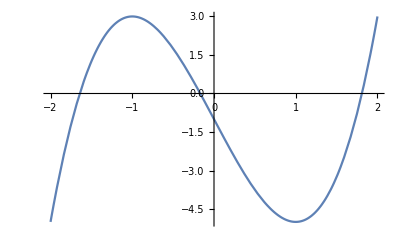

```mathematica
s=NSolve[2x^3-6x-1==0,x]
Plot[2x^3-6x-1==0,{x,-2,2}]
```

(1+6 x)/(2 x^2)

{-0.887015,103.971,-1.08432}

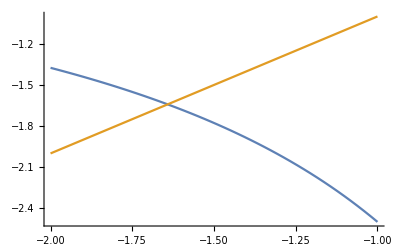

```mathematica
g1[x_]=(6x+1)/(2x^2)
g1'[x/.s]
Plot[{g1[x],x},{x,-2,-1}]
```

(1+2 x)/(-4+2 x^2)

{-6.31373,-0.478463,-4.35066}

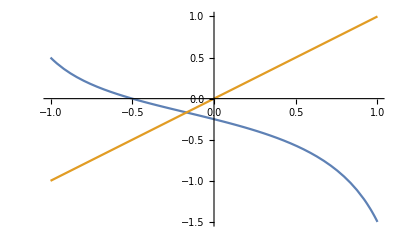

```mathematica
g2[x_]=(2x+1)/(2x^2-4)
g2'[x/.s]
Plot[{g2[x],x},{x,-1,1}]
```

(1+6 x-x^3)^(1/3)

{0.129005+0.223443 ⅈ,-34.8238-60.3166 ⅈ,-0.389544}

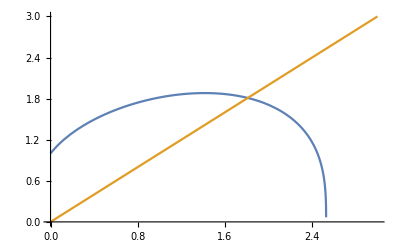

```mathematica
g3[x_]=(-x^3+6x+1)^(1/3)
g3'[x/.s]
Plot[{g3[x],x},{x,0,3}]
```